# Loop Equations Bootstrap

Okay, a little introduction to what we’re trying to do. This code generates the figures for section 4 — Bootstrapping 1-matrix models. For simplicity, we start with the single Hermitian matrix model:

V(ϕ)=1/2 ϕ^2+ 1/4 g ϕ^4

This is page 7 in the paper, equation 4.14. From that same page:

“We will take the search space S to be a single parameter t_2≥ 0 and set all odd correlation functions to zero.”

We follow the general approach outlined above to derive constraints. In other words:

- starting from some value of t_2, we use the loop equations to compute all correlations up to some power 2d
- We assemble these correlators into the inner product matrix M_dxd,
- and find the region where all its eigenvalues are positive.

### Analytics and Exact Solutions

I think these are exact solutions to a few cases below.

```mathematica
c2[g_]:=Module[{a=Sqrt[1/(6 g)((1+12g)^(1/2)-1)]},1/3 a^2(4-a^2)];
c2[0]=1;
c2::usage = "This is, I believe, an exact solution for negative g, ie, when the potential V is unbounded from below.

exact solution for t_4";

c4[g_]:=Module[{a=Sqrt[1/(6 g)((1+12g)^(1/2)-1)]},1/2 a^4(6-2a^2)];
c4::usage = "-a^2 + 3 a^4 with the same value for a as above. Interesting.

exact solution for t_4";
```

```mathematica
ρ[g_,λ_]:=Module[{a2=2/(3 g)(-1+Sqrt[1+12 g])},-I/(2π)(g λ^2+g a2/2+1)Sqrt[λ^2-a2] ];
ρ::usage = "Eigenvalue distribution, see paper for references.";
```

### Loop Equations

Now let' s define the loop equations for the single matrix model. I’m not going to derive this here, since I can’t type quickly yet in Mathematica... but the following function generates correlators for the single matrix model described in the doc string. This is key, of course.

TODO add a derivation in here, showing why, for the single matrix model, the following recursive definition makes sense.

Definitions for t_0 through t_2 are enough to generate everything else. If you set t_1 to 0, for example, that’s enough to set all odd-indexed correlators to zero.

```mathematica
singleMatrixCorrelators[maxIdx_,t_] := 
With[{max=Max[maxIdx -3, 0]},
Do[Subscript[t, k+3]=Simplify[1/g(Sum[Subscript[t, l] Subscript[t, k-l-1],{l,0,k-1}]-Subscript[t, k+1])],{k,Range[0,max]}]];
singleMatrixCorrelators::usage = "singleMatrixCorrelators[maxIdx, t] populates t's subscripts with a correlator for each subscript, up to t_maxIdx. These correlators are for the single matrix model of the form V(M) =1/2M^2 +g/4M^4.";
```

NOTES on the sum:

* I’ve changed the indices vs the original code, so now correlators has every term, and the odd terms all equal 0.
* We have this nice property that if you set t_1=0, all of the odd terms become 0, all the way up. Why? Well, look at the summation. If k is even (which means, somehow, that we’re calculating the EVEN traces...), then k-1 is odd... odd + even = odd, even + odd = odd, so you’ll always have an odd term in every element of the summation.

### A view of the peninsula

This section will give us a view of... the peninsula, as described. First let’s reset our variables for the next section.

```mathematica
Clear[g]; Remove[t];
```

t_0=1, I forget why, but fill this in.

We’ll also set  t_1 = 0, which will kill all odd correlators; this makes the example more straightforward to calculate and display. Keeping these correlators in would constrain the region more fully.

```mathematica
Subscript[t, 0]=1;
Subscript[t, 1] = 0;
```

Now let's generate even correlators up to some maximum level:

```mathematica
maxIdx = 72;
singleMatrixCorrelators[maxIdx, t];
```

Then let’s force the evaluation of each of these correlators and store them in a list, indexed by their subscripts.

```mathematica
correlators=Table[ Evaluate[ Subscript[t, k]],{k,Range[1,maxIdx]} ];
```

Finally, take three examples for graphing. I think we actually want to make a function that generates a plot for each example, but let’s start with this.

```mathematica
tk=correlators[[32]];
tk1=correlators[[52]];
tk2=correlators[[72]];
```

Here’s an example:

```mathematica
correlators[[4]]
```

(1-t_2)/g

### Peninsula Plots

Now, we get into Henry’s peninsula plots. Here’s the code to generate one of the gray overlays.

```mathematica
generatePlot[eq_, gRange_, tRange_] := 
Module[{defaults=  List[
PlotPoints->200,
PlotRange->tRange,
PlotStyle->{Opacity[0],
Opacity[0]},Filling->{1->{2}},
FillingStyle->{Opacity[0.15],Gray}]},
Plot[{
Solve[eq==0][[1,1,2]],
Solve[eq==0][[2,1,2]]
},Prepend[gRange, g], Evaluate[defaults]]];
generatePlot::usage = "Generate an overlay for the peninsula plot.";

trueSolution[f_, gRange_, tRange_] :=
Module[{defaults=List[
PlotPoints->200,
PlotRange->tRange,
PlotStyle->{Darker@Green,Thickness[0.004]}
]},
Plot[f[g],Prepend[gRange, g],Evaluate[defaults]]];
trueSolution::usage = "Plot the true solution.";

tgLabel[plot_] := 
Labeled[plot,{"tr M^2","g"},{Left,Bottom}];
```

Figure bounds:

```mathematica
gRange = {-0.09,0};
tRange = {0.9,3};
```

And some more:

```mathematica
plots = generatePlot[#, gRange, tRange]& /@ {tk, tk1, tk2};
```

General::munfl: (-1.39958×10^-7)^50 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.39958×10^-7)^51 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.39958×10^-7)^52 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Group them into a final plot:

```mathematica
cplot= trueSolution[c2, gRange, tRange];
```

And here we go with the final:

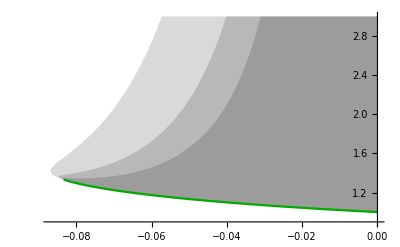
-Graphics-tr M^2g

```mathematica
Show@Append[plots, cplot] // tgLabel
```

### RegionPlot

And the same thing with RegionPlot:

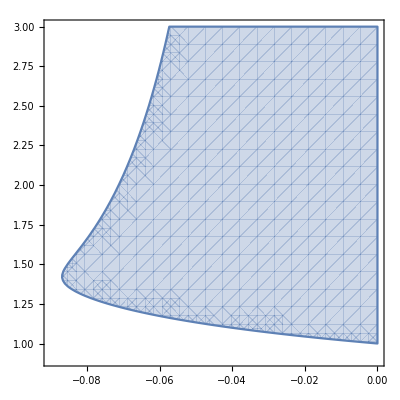
-Graphics-tr M^2g

```mathematica
RegionPlot[tk ≥ 0 , {g, -0.09, 0}, {Subscript[t, 2], 0.9, 3}] // tgLabel
```

This is the same thing, but plotting the intersection of ALL of the correlators, alongside the three chosen for the peninsula.

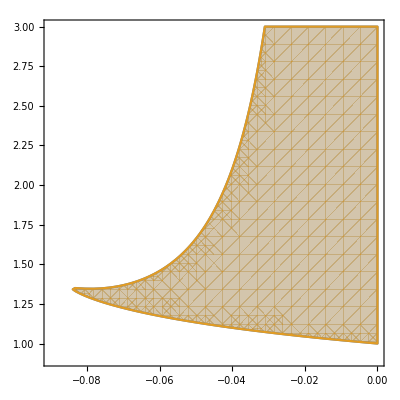
-Graphics-tr M^2g

```mathematica
ks = Function[f, f ≥ 0] /@ correlators;
RegionPlot[{Fold[And, ks], tk ≥ 0 && tk1 ≥ 0 && tk2 ≥ 0}, {g, -0.09, 0}, {Subscript[t, 2], 0.9, 3}] // tgLabel
```

Okay, good, got that figured out. Now I get what’s happening, though I don’t quite get the trick with the solve syntax. On to the next thing.

## Next Area

```mathematica
tk2/.{g->3.0,Subscript[t, 2]->0.7}
```

9.45694

```mathematica
Expand[(X-a)^4]
```

a^4-4 a^3 X+6 a^2 X^2-4 a X^3+X^4

```mathematica
m={{Subscript[t, 2j],Subscript[t, j+k]},{Subscript[t, j+k],Subscript[t, 2k]}}
```

{{t_(2 j),t_(j+k)},{t_(j+k),t_(2 k)}}

```mathematica
Eigenvalues[m]//FullSimplify
```

{1/2 (t_(2 j)+t_(2 k)-√((t_(2 j)-t_(2 k))^2+4 t_(j+k)^2)),1/2 (t_(2 j)+t_(2 k)+√((t_(2 j)-t_(2 k))^2+4 t_(j+k)^2))}

```mathematica
1/4 (1+x2m-√(1-2 x2m+x2m^2+4 xm^2))^2//Expand
```

1/2+x2m^2/2+xm^2-1/2 √(1-2 x2m+x2m^2+4 xm^2)-1/2 x2m √(1-2 x2m+x2m^2+4 xm^2)

## Fingers plot

Get these variables set up:

```mathematica
t72=correlators[[72]];
t68=correlators[[68]];
t8=correlators[[8]];
```

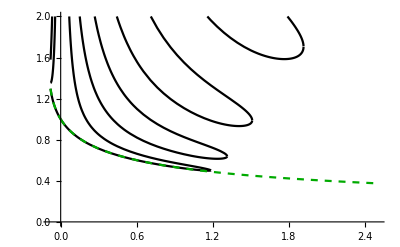

```mathematica
p=Plot[
{Solve[t68==0][[;;,1,2]],c2[g]},{g,-0.08,2.5},
PerformanceGoal->"Quality",
PlotRange->{0,2},
PlotStyle->{Black,{Darker@Green,Dashed}},
Filling->{4->{2}},
AspectRatio-> 0.6180339887498948]
```

Seems very similar, maybe with a difference of precision and the indices provided to t68.

```mathematica
Show[Plot[
{Solve[t68==0]⟦1;;All,1,2⟧,c2[g]},{g,-0.08,2.5},
PerformanceGoal->"Quality",
PlotRange->{0,2},
PlotStyle->{Black,{Darker[Green],Dashed}},
Filling->{4->{2}}],
AspectRatio->0.6180339887498948]
```

-Graphics-

TODO - figure out how to pass args through.

```mathematica
fingersPlot[idx_] := Module[
{varName =  ToString[Subscript["t",idx],StandardForm]},
RegionPlot[
{correlators[[idx]]>0},{g,0,2.6},{Subscript[t, 2],-0.1,2.1},
PlotPoints->100,
PlotLegends->{varName<>" > 0"},
PlotStyle->Opacity[0.1]
]];
fingersPlot::usage = "Plot a fingers plot.";
```

Now let’s get these calculated:

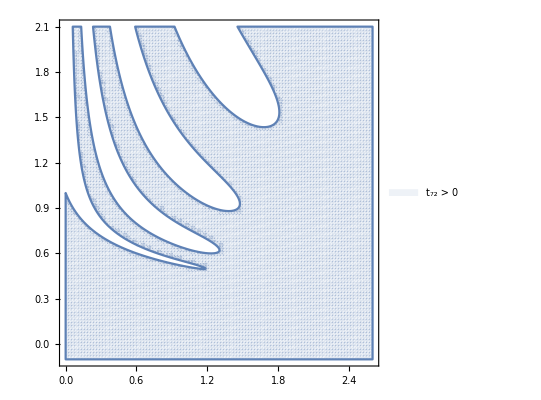

```mathematica
rp72=fingersPlot[72]
```

I did the next two manually.

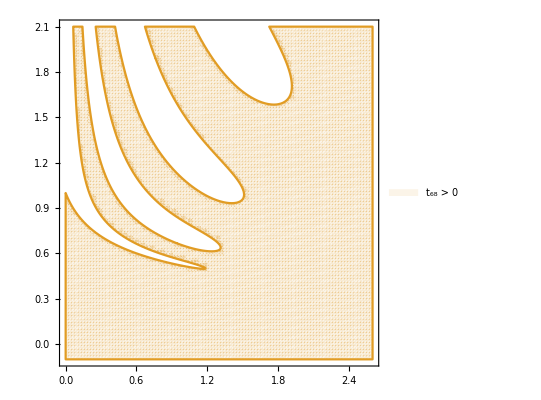

```mathematica
rp68=RegionPlot[
{correlators[[68]]>0},{g,0,2.6},{Subscript[t, 2],-0.1,2.1},
PlotPoints->100,
PlotLegends->{"t_68 > 0"},
PlotStyle->{Directive[ColorData[97,"ColorList"][[2]],Opacity[0.1]]},
BoundaryStyle->ColorData[97,"ColorList"][[2]]
]
```

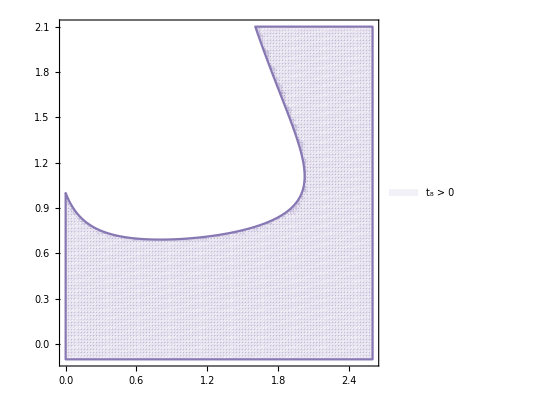

```mathematica
rp8=RegionPlot[
{correlators[[8]]>0},{g,0,2.6},{Subscript[t, 2],-0.1,2.1},
PlotPoints->100,
PlotLegends->{"t_8 > 0"},
PlotStyle->{Directive[ColorData[97,"ColorList"][[5]],Opacity[0.1]]},
BoundaryStyle->ColorData[97,"ColorList"][[5]]
]
```

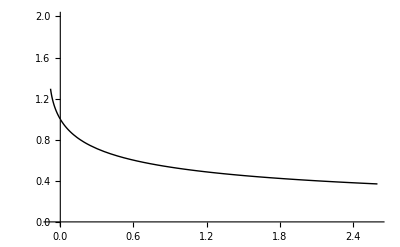

```mathematica
exact=Plot[
c2[g],{g,-0.08,2.6},
PerformanceGoal->"Quality",PlotRange->{0,2},
PlotStyle->{Thick,Black},
Filling->{4->{2}}]
```

```mathematica
Labeled[
Show[rp72,rp68,rp8,exact,
PlotRange->{{0.05,2.5},{0,2.0}},
AspectRatio->0.6180339887498948],{"tr M^2"},{Left}]
```

-Graphics-tr M^2

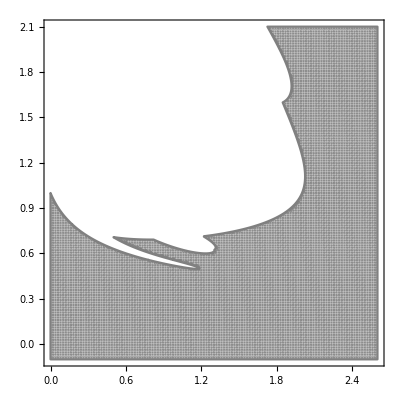

```mathematica
rpInt=RegionPlot[
{t8>0&&t68>0&&t72>0},{g,0,2.6},{Subscript[t, 2],-0.1,2.1},
PlotPoints->200,
PlotStyle->{Opacity[0.3],Gray},
BoundaryStyle->Gray]
```

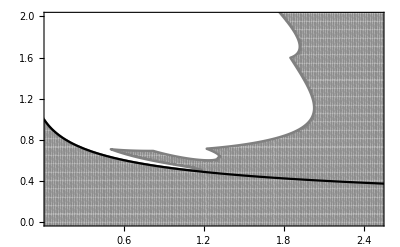
-Graphics-tr M^2g

```mathematica
Show[rpInt,exact,PlotRange->{{0.05,2.5},{0,2.0}},
AspectRatio->0.6180339887498948] // tgLabel
```

```mathematica
Show[rpInt,exact,PlotRange->{{0.05,2.5},{0,2.0}},AspectRatio->0.6180339887498948] // tgLabel
```

-Graphics-tr M^2g

```mathematica
Show[rp72,rp68,rp8,exact,PlotRange->{{0.05,2.5},{0,2.0}},AspectRatio->0.6180339887498948]
```

-Graphics-

```mathematica
tgLabel[p]
```

-Graphics-tr M^2g

## Fancy method

OKAY, let’s do the fancy method now. I’m finally to the goods.

Let’s generate some helper functions.

```mathematica
innerProductMatrix[t_, N_] := Table[Subscript[t, j+k], {j, 0, N - 1}, {k, 0, N - 1}]
innerProductMatrix::usage = "Generate the NxN inner producty matrix built from correlators in t.";

upperLeftM[M_, N_] := MatrixForm[M[[1;;N,1;;N]]];
upperLeftM::usage = "Prints the upper-left NxN submatrix of M in matrix form.";

generateSolutions[M_, gVal_] :=
Module[
{detM=Det[M/.{g->gVal}] /. Subscript[t, 2] -> t2},
NSolve[detM==0,t2,Reals][[;;,1,2]]]
generateSolutions::usage = "Returns all solutions for t_2.";

datTable[M_, res_, jRange_] := 
Table[
{j*res, generateSolutions[M, j * res]},
{j, jRange}];

map2[xs_, f_] := Transpose @ {
xs[[;;, 1]], f /@ xs[[;;, 2]]
};
map2::usage = "maps a function across the second element in the pair.";

nthSolution[solutions_, n_] := solutions[[n]];

extractSolutions[xs_, n_] := Sort @ map2[xs, nthSolution[#, n]&];
```

Okay, what is going on here. We:

- generate the inner product matrix
- scan through cM, generating the determinant at each point.
- the bounds in this case are [-34/400,-1/400] because of this resolution.
- SO that tells us that that part should not matter for the final graph.

here we do an 8x8 matrix:

```mathematica
M8=innerProductMatrix[t, 8];
```

Let' s see a submatrix as an example of the form:

```mathematica
upperLeftM[M8, 4]
```

(1 | 0 | t_2 | 0
0 | t_2 | 0 | (1-t_2)/g
t_2 | 0 | (1-t_2)/g | 0
0 | (1-t_2)/g | 0 | (-1+(1+2 g) t_2)/g^2)

```mathematica
resolution=1/400
datM8=datTable[M8, resolution, Range[-34,-1]];
```

1/400

Show off some of the values...

```mathematica
Take[datM8, 2]
```

{{-17/200,{-8.61996,0.823212,1.10351,1.34954,1.35448,1.41793,1.49936,10.6612,11.7582,13.1517}},{-33/400,{-8.75854,0.824651,1.09979,1.3194,1.32109,1.41504,1.50809,11.0214,12.115,13.4988}}}

Now let' s extract the 5th and 6 solutions. Why these?

```mathematica
lowerBoundM8=extractSolutions[datM8, 5];
upperBoundM8=extractSolutions[datM8, 6];
```

```mathematica
smallestEigenvalue[M_] := 
First[-Eigenvalues[-M,1,Method->{"Arnoldi","Criteria"->"RealPart"}]]
```

So we have evidence here that c2 above is, again, the exact solution... but what about p?
Here’s one of the upper left matrices:

```mathematica
upperLeftM[M8, 4]
```

(1 | 0 | t_2 | 0
0 | t_2 | 0 | (1-t_2)/g
t_2 | 0 | (1-t_2)/g | 0
0 | (1-t_2)/g | 0 | (-1+(1+2 g) t_2)/g^2)

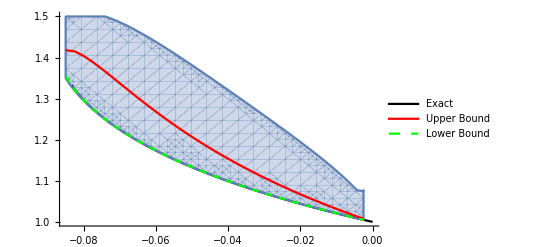

```mathematica
Show[
Plot[{c2[x]},{x,-1/10,0},
PlotStyle->{Black},
PlotLegends->{"Exact"},
GridLines->{{0,-1/12}},
PlotRange->All 
],
RegionPlot[
PositiveSemidefiniteMatrixQ[innerProductMatrix[t,7]]
, {g, -34/400, -1/400}, {Subscript[t, 2], 0.9, 1.5},
PerformanceGoal->"Quality"],
ListPlot[{upperBoundM8,lowerBoundM8},
Joined->True,
InterpolationOrder->1,
PlotStyle->{Red,{Green,Dashed}},
PlotLegends->{"Upper Bound"," Lower Bound"}]]
```

That worked well ... but what is going on with that plucking out of the solutions?

```mathematica
smallestEigenvalue[M10 /. g -> -0.09 /. Subscript[t, 2] -> 1.1]
```

-0.0000112887

### Bigger Matrix - 10x10

Let’s try again with a 10x10 matrix. (NOTE for Henry - where is the power of g coming from? Why does it not matter for solutions?)

```mathematica
M10=innerProductMatrix[t, 10];
```

Now, some more shenanigans to understand.

```mathematica
(*TODO - get this better resolution and range interaction up into datTable. Rename datTable.*)
jMax=2;
resolution=1/50;
posM10=datTable[M10, resolution, Range[1, jMax/resolution]];
negM10 = datTable[M10, 1/200, Range[-20, -1]];
```

Now get some graphs going.

```mathematica
upperBoundM10=Sort@Join[
extractSolutions[negM10, 8],
{{0,1}},
extractSolutions[posM10, 9]];
lowerBoundM10=Sort@Join[
extractSolutions[negM10, 7],
{{0,1}},
extractSolutions[posM10, 8]
];
```

Part::partw: Part 8 of {-1.58856,0,1.28328,1.38197,3.61803,5.86995,10.0007} does not exist.

Part::partw: Part 8 of {-1.6218,0,1.26112,1.34237,3.92078,6.30336,10.527} does not exist.

Part::partw: Part 8 of {-1.65753,0,1.24045,1.30792,4.24764,6.7825,11.1117} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
exact={#,N[c2@#]}&/@upperBoundM10[[;;,1]];
```

```mathematica
exact[[2]]
```

{-19/200,1.45686-0.107486 ⅈ}

Part::partw: Part 8 of {-1.58856,0.,1.28328,1.38197,3.61803,5.86995,10.0007} does not exist.

Part::partw: Part 8 of {-1.6218,0.,1.26112,1.34237,3.92078,6.30336,10.527} does not exist.

Part::partw: Part 8 of {-1.65753,0.,1.24045,1.30792,4.24764,6.7825,11.1117} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

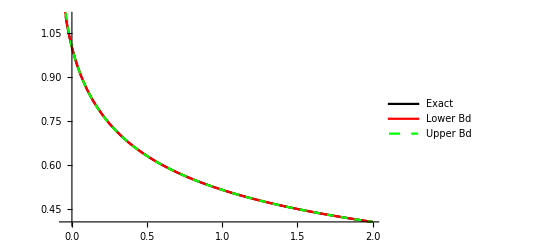
-Graphics-tr M^2g

```mathematica
Show[Plot[{c2[x]},{x,-1/24,2},
PlotStyle->{Black},
PlotLegends->{"Exact"},
GridLines->{{0,-1/12}}],
RegionPlot[
PositiveSemidefiniteMatrixQ[innerProductMatrix[t, 10]]
, {g, -0.1, 2}, {Subscript[t, 2],  0.4, 1.2},
PerformanceGoal->"Quality"],
ListPlot[{lowerBoundM10,upperBoundM10},
Joined->True,
PlotStyle->{Red,{Green,Dashed}},
PlotLegends->{"Lower Bd"," Upper Bd"}]] // tgLabel
```

### Error Bounds

```mathematica
upperr=Table[{exact[[i,1]],upp[[i,2]]-exact[[i,2]]},{i,1,Length@exact}];
downerr=Table[{exact[[i,1]],downn[[i,2]]-exact[[i,2]]},{i,1,Length@exact}];
```

Nice plots

```mathematica
jm=5;res=1/100;
```

```mathematica
d=4;
dat6=Table[{j*res,detM=Det[cM[[;;d,;;d]]/.{g->j*res}]/.{Subscript[t, 2]->t2};Normal@NSolve[detM==0,t2,Reals][[;;,1,2]]},{j,1,jm/res}];
PrependTo[dat7,{0,ConstantArray[1,Length[dat7[[1,2]]]]}];
```

```mathematica
d=5;
dat7=Table[{j*res,detM=Det[cM[[;;d,;;d]]/.{g->j*res}]/.{Subscript[t, 2]->t2};Normal@NSolve[detM==0,t2,Reals][[;;,1,2]]},{j,1,jm/res}];
PrependTo[dat7,{0,ConstantArray[1,Length[dat7[[1,2]]]]}];
```

```mathematica
d=6;
dat8=Table[{j*res,detM=Det[cM[[;;d,;;d]]/.{g->j*res}]/.{Subscript[t, 2]->t2};Normal@NSolve[detM==0,t2,Reals][[;;,1,2]]},{j,1,jm/res}];
PrependTo[dat8,{0,ConstantArray[1,Length[dat8[[1,2]]]]}];
```

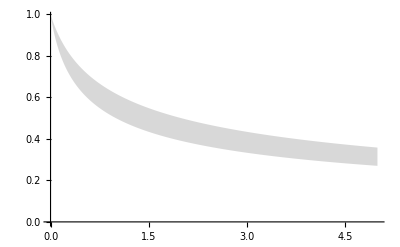

```mathematica
up6=Transpose@{dat6[[;;,1]],dat6[[;;,2,-1]]};
down6=Transpose@{dat6[[;;,1]],dat6[[;;,2,-2]]};
l6=ListPlot[{down6,up6},Joined->True,InterpolationOrder->2,PlotStyle->{Opacity[0],Opacity[0]},Filling->{1->{2}},FillingStyle->Directive[Gray,Opacity[0.3]],PerformanceGoal->"Quality"]
```

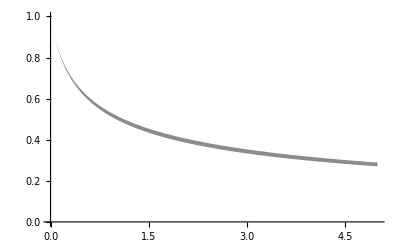

```mathematica
up7=Transpose@{dat7[[;;,1]],dat7[[;;,2,-1]]};
down7=Transpose@{dat7[[;;,1]],dat7[[;;,2,-2]]};
l7=ListPlot[{down7,up7},Joined->True,InterpolationOrder->2,PlotStyle->{Opacity[0],Opacity[0]},Filling->{1->{2}},FillingStyle->Directive[Gray,Opacity[0.9]],PerformanceGoal->"Quality"]
```

```mathematica
up8=Transpose@{dat8[[;;,1]],dat8[[;;,2,-3]]};
down8=Transpose@{dat8[[;;,1]],dat8[[;;,2,-2]]};
l8=ListPlot[{down8,up8},Joined->True,InterpolationOrder->2,PlotStyle->{Opacity[0],Opacity[0]},Filling->{1->{2}},FillingStyle->Black,PerformanceGoal->"Quality"]
```

-Graphics-